## L=4*4

## vary density, β=16

```mathematica
ndca={1.3,1.25,1.2,1.15,1.1,1.05,1,0.95,0.9,0.85,0.8,0.75,0.7};
```

```mathematica
WeightNNdd={0.521807252,0.567117164,0.558332583,0.526009574,0.499542759,0.478578369,0.526737374,0.604372099,0.637188576,0.678104311,0.696934539,0.709579058,0.719954608};
WeightNNdL={0.273494619,0.293035949,0.278230144,0.24384427,0.204095006,0.16151239,0.157865317,0.198099107,0.213713875,0.227625015,0.227992069,0.231481704,0.223164872};
WeightNNLL={0.068094795,0.07336977,0.062488888,0.047477724,0.033114871,0.021316961,0.019155955,0.023646387,0.025068921,0.026767356,0.025830137,0.026511266,0.024028608};
WeightNNtotal2={0.864895577,0.934779749,0.900219252,0.818261918,0.737466461,0.66186925,0.704078593,0.826478616,0.876358049,0.932908623,0.951125219,0.967900092,0.967462749};
WeightNNtotal2vsn=Table[{ndca[[i]],WeightNNtotal2[[i]]},{i,1,13}];
WeightNNddvsn=Table[{ndca[[i]],WeightNNdd[[i]]/WeightNNtotal2[[i]]},{i,1,13}];
WeightNNdLvsn=Table[{ndca[[i]],WeightNNdL[[i]]/WeightNNtotal2[[i]]},{i,1,13}];
WeightNNLLvsn=Table[{ndca[[i]],WeightNNLL[[i]]/WeightNNtotal2[[i]]},{i,1,13}];
```

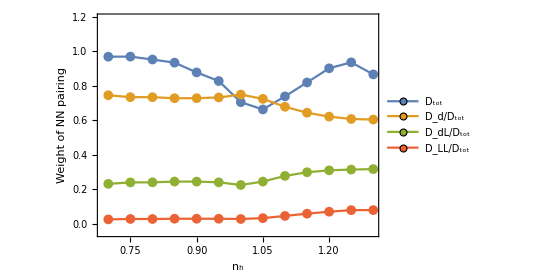

```mathematica
Weightvsn1=ListPlot[{WeightNNtotal2vsn,WeightNNddvsn,WeightNNdLvsn,WeightNNLLvsn},PlotLegends->Placed[LineLegend[{"D_tot","D_d/D_tot","D_dL/D_tot","D_LL/D_tot"},LabelStyle->{FontFamily->"Arial",15},LegendLayout->{"Row",1},LegendMarkerSize->11],{0.5,0.93}],Frame->True,AspectRatio->0.7,BaseStyle->{FontSize->18,FontFamily->"Arial"},PlotRange->{Automatic,{-0.05,1.19}},FrameLabel->{Subscript[n,h],"Weight of NN pairing"},LabelStyle->{FontFamily->"Arial"},PlotMarkers->{Graphics[Disk[]],10},Joined->True]
```